```mathematica
SetDirectory[NotebookDirectory[]];
dataJac=Import["fileJac.dat"];
```

```mathematica
g1Jac:=Plot3D[(1-x)x Sin[Pi y],{x,0,1},{y,0,1}]
```

```mathematica
g2Jac:=ListPlot3D[dataJac,DataRange->{{0,1},{0,1}},PlotStyle->Red]
```

```mathematica
Show[g1Jac,g2Jac]
```

-Graphics3D-

```mathematica
dataZeid=Import["fileZeid.dat"];
g1Zeid:=Plot3D[(1-x)x Sin[Pi y],{x,0,1},{y,0,1}]
g2Zeid:=ListPlot3D[dataZeid,DataRange->{{0,1},{0,1}},PlotStyle->Red]
Show[g1Zeid,g2Zeid]
```

-Graphics3D-

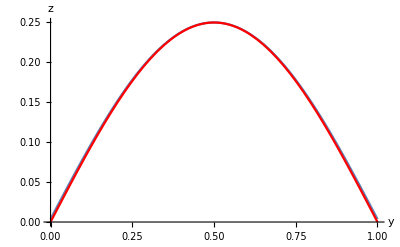

```mathematica
Show[ListLinePlot[dataZeid[[100]],DataRange->{0,1}],Plot[(1-100/212)100/212 Sin[Pi*y],{y,0,1},PlotStyle->Red],AxesLabel->{"y","z"}]
```